```mathematica
ClearAll["Global`*"]
```

Define the probability matrix

```mathematica
P = {{1-c, 0, c, 0, 0}, {s*(1-c), (1-c)*(1-s), c*s, c*(1-s), 0}, {0, w*(1-c), (1-w), c*w, 0}, {0, (1-c)*s*w, (1-w)*s, (1-w)*(1-s)+c*w*s, w*(1-s)}, {0, s*(1-c), 0, s*c, 1-s}};
```

Check the eigenvalues of P, of interest is only the left eigenvector corresponding to an eigenvalue of 1.

```mathematica
Eigenvalues[P]//Simplify
```

{1,Root[1-2 c+c^2-3 s+6 c s-3 c^2 s+3 s^2-6 c s^2+3 c^2 s^2-s^3+2 c s^3-c^2 s^3-2 w+4 c w-2 c^2 w+6 s w-12 c s w+6 c^2 s w-6 s^2 w+12 c s^2 w-6 c^2 s^2 w+2 s^3 w-4 c s^3 w+2 c^2 s^3 w+w^2-2 c w^2+c^2 w^2-3 s w^2+6 c s w^2-3 c^2 s w^2+3 s^2 w^2-6 c s^2 w^2+3 c^2 s^2 w^2-s^3 w^2+2 c s^3 w^2-c^2 s^3 w^2+(-4+6 c-2 c^2+9 s-13 c s+4 c^2 s-6 s^2+8 c s^2-2 c^2 s^2+s^3-c s^3+6 w-8 c w+2 c^2 w-13 s w+18 c s w-5 c^2 s w+8 s^2 w-11 c s^2 w+3 c^2 s^2 w-s^3 w+c s^3 w-2 w^2+2 c w^2+4 s w^2-5 c s w^2+c^2 s w^2-2 s^2 w^2+3 c s^2 w^2-c^2 s^2 w^2) #1+(6-6 c+c^2-9 s+8 c s-c^2 s+3 s^2-2 c s^2-6 w+4 c w+8 s w-5 c s w-2 s^2 w+c s^2 w+w^2-s w^2) #1^2+(-4+2 c+3 s-c s+2 w-s w-c s w) #1^3+#1^4&,1],Root[1-2 c+c^2-3 s+6 c s-3 c^2 s+3 s^2-6 c s^2+3 c^2 s^2-s^3+2 c s^3-c^2 s^3-2 w+4 c w-2 c^2 w+6 s w-12 c s w+6 c^2 s w-6 s^2 w+12 c s^2 w-6 c^2 s^2 w+2 s^3 w-4 c s^3 w+2 c^2 s^3 w+w^2-2 c w^2+c^2 w^2-3 s w^2+6 c s w^2-3 c^2 s w^2+3 s^2 w^2-6 c s^2 w^2+3 c^2 s^2 w^2-s^3 w^2+2 c s^3 w^2-c^2 s^3 w^2+(-4+6 c-2 c^2+9 s-13 c s+4 c^2 s-6 s^2+8 c s^2-2 c^2 s^2+s^3-c s^3+6 w-8 c w+2 c^2 w-13 s w+18 c s w-5 c^2 s w+8 s^2 w-11 c s^2 w+3 c^2 s^2 w-s^3 w+c s^3 w-2 w^2+2 c w^2+4 s w^2-5 c s w^2+c^2 s w^2-2 s^2 w^2+3 c s^2 w^2-c^2 s^2 w^2) #1+(6-6 c+c^2-9 s+8 c s-c^2 s+3 s^2-2 c s^2-6 w+4 c w+8 s w-5 c s w-2 s^2 w+c s^2 w+w^2-s w^2) #1^2+(-4+2 c+3 s-c s+2 w-s w-c s w) #1^3+#1^4&,2],Root[1-2 c+c^2-3 s+6 c s-3 c^2 s+3 s^2-6 c s^2+3 c^2 s^2-s^3+2 c s^3-c^2 s^3-2 w+4 c w-2 c^2 w+6 s w-12 c s w+6 c^2 s w-6 s^2 w+12 c s^2 w-6 c^2 s^2 w+2 s^3 w-4 c s^3 w+2 c^2 s^3 w+w^2-2 c w^2+c^2 w^2-3 s w^2+6 c s w^2-3 c^2 s w^2+3 s^2 w^2-6 c s^2 w^2+3 c^2 s^2 w^2-s^3 w^2+2 c s^3 w^2-c^2 s^3 w^2+(-4+6 c-2 c^2+9 s-13 c s+4 c^2 s-6 s^2+8 c s^2-2 c^2 s^2+s^3-c s^3+6 w-8 c w+2 c^2 w-13 s w+18 c s w-5 c^2 s w+8 s^2 w-11 c s^2 w+3 c^2 s^2 w-s^3 w+c s^3 w-2 w^2+2 c w^2+4 s w^2-5 c s w^2+c^2 s w^2-2 s^2 w^2+3 c s^2 w^2-c^2 s^2 w^2) #1+(6-6 c+c^2-9 s+8 c s-c^2 s+3 s^2-2 c s^2-6 w+4 c w+8 s w-5 c s w-2 s^2 w+c s^2 w+w^2-s w^2) #1^2+(-4+2 c+3 s-c s+2 w-s w-c s w) #1^3+#1^4&,3],Root[1-2 c+c^2-3 s+6 c s-3 c^2 s+3 s^2-6 c s^2+3 c^2 s^2-s^3+2 c s^3-c^2 s^3-2 w+4 c w-2 c^2 w+6 s w-12 c s w+6 c^2 s w-6 s^2 w+12 c s^2 w-6 c^2 s^2 w+2 s^3 w-4 c s^3 w+2 c^2 s^3 w+w^2-2 c w^2+c^2 w^2-3 s w^2+6 c s w^2-3 c^2 s w^2+3 s^2 w^2-6 c s^2 w^2+3 c^2 s^2 w^2-s^3 w^2+2 c s^3 w^2-c^2 s^3 w^2+(-4+6 c-2 c^2+9 s-13 c s+4 c^2 s-6 s^2+8 c s^2-2 c^2 s^2+s^3-c s^3+6 w-8 c w+2 c^2 w-13 s w+18 c s w-5 c^2 s w+8 s^2 w-11 c s^2 w+3 c^2 s^2 w-s^3 w+c s^3 w-2 w^2+2 c w^2+4 s w^2-5 c s w^2+c^2 s w^2-2 s^2 w^2+3 c s^2 w^2-c^2 s^2 w^2) #1+(6-6 c+c^2-9 s+8 c s-c^2 s+3 s^2-2 c s^2-6 w+4 c w+8 s w-5 c s w-2 s^2 w+c s^2 w+w^2-s w^2) #1^2+(-4+2 c+3 s-c s+2 w-s w-c s w) #1^3+#1^4&,4]}

Find the left eigenvector corresponding to eigenvalue 1 (Left eigenvector is the right eigenvector if the transpose of the matrix).

```mathematica
StaticD=Eigenvectors[Transpose[P]][[1]]//Simplify;
```

Normalize the eigenvector such that the sum of its elements is 1.

```mathematica
StaticD =StaticD/Total[StaticD] //Simplify
```

{((-1+c)^2 s^2 (s (-1+w)-w) w)/(s^2 (s (-1+w)-w) w+c^2 (-1+s) (s^2 (-1+w)^2-s (-1+w) w+w^2)-c s (s (2-3 w) w+w^2+s^2 (1-3 w+2 w^2))),-((-1+c) c s (s (-1+w)-w) w)/(s^2 (s (-1+w)-w) w+c^2 (-1+s) (s^2 (-1+w)^2-s (-1+w) w+w^2)-c s (s (2-3 w) w+w^2+s^2 (1-3 w+2 w^2))),-(c s^2 (c+s+c s (-1+w)+w-2 c w-s w))/(s^2 (s (-1+w)-w) w+c^2 (-1+s) (s^2 (-1+w)^2-s (-1+w) w+w^2)-c s (s (2-3 w) w+w^2+s^2 (1-3 w+2 w^2))),-(c^2 s w)/(s^2 (s (-1+w)-w) w+c^2 (-1+s) (s^2 (-1+w)^2-s (-1+w) w+w^2)-c s (s (2-3 w) w+w^2+s^2 (1-3 w+2 w^2))),(c^2 (-1+s) w^2)/(s^2 (s (-1+w)-w) w+c^2 (-1+s) (s^2 (-1+w)^2-s (-1+w) w+w^2)-c s (s (2-3 w) w+w^2+s^2 (1-3 w+2 w^2)))}

Sum the probabilities that the state of the saloon is such that the first chair is busy (a customer coming will not be serviced and go away)

```mathematica
PB = StaticD[[3]]+ StaticD[[4]]+ StaticD[[5]];
```

Assume values for s and w, and plot the dependency on c

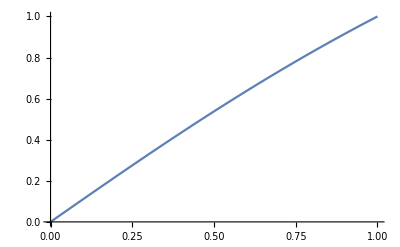

```mathematica
s = 0.9; 
w =0.9; 
Plot[PB, {c, 0, 1}, PlotRange->{0,1}]
```

Assume values for s and w, and plot the dependency on w

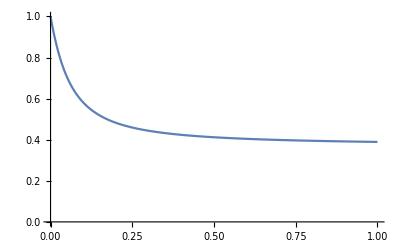

```mathematica
c= 0.1; 
s =0.1; 
Plot[PB, {w, 0, 1}, PlotRange->{0, 1}]
```

Assume values for c and w, and plot the dependency on s

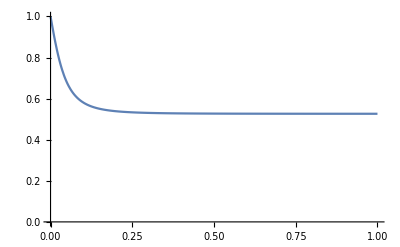

```mathematica
c= 0.1; 
w =0.1; 
Plot[PB, {s, 0, 1}, PlotRange->{0, 1}]
```

Assume some probability values. c -> Probability of a customer coming, s-> probability of styling done, w->probability of washing done

```mathematica
c = 0.1;
s = 0.9;
w = 0.9;
```

Check what is the probability distribution of the states

```mathematica
StaticD
```

{0.791427,0.097707,0.0988036,0.010966,0.0010966}

Check what is the probability that a customer will not be serviced

```mathematica
PB
```

0.110866

```mathematica
Clear[c, s, w]
```